```mathematica
Clear["Global`*"]
(* Initialization *)
σ = 10; b = 8/3; r =28;
f[x_, y_, z_] := σ*(y- x);
g[x_, y_, z_] := r*x - y -x*z;
h[x_, y_, z_] := x*y - b*z;
J[x_, y_, z_] := {{D[f[x,y,z],x],D[f[x,y,z],y], D[f[x,y,z],z]}, {D[g[x,y,z],x],D[g[x,y,z],y], D[g[x,y,z],z]},{D[h[x,y,z],x], D[h[x,y,z],y],D[h[x,y,z],z]}}
Tmax = 1000; Tmin = 1;
s=NDSolve[{x'[t]==σ*(y[t]-x[t]),y'[t]==r*x[t]-y[t]-x [t]*z[t],z'[t]==x[t]*y[t] - b*z[t],x[0]==y[0]==z[0]==0.01},{x,y,z},{t,0,Tmax}, Method->"ExplicitRungeKutta"];
dt = 0.001;
Q = IdentityMatrix[3];
λ = ConstantArray[0,3];
lambdaList = {{0,0,0}};
plotIndex = 0;
(* Main loop *)
For[i=Tmin,i<Tmax,i = i + dt,
trajI ={Evaluate[x[i]/. s],  Evaluate[y[i]/. s],Evaluate[z[i]/. s]};
	Jxt = J[x, y, z] /. {x -> trajI[[1]][[1]], y-> trajI[[2]][[1]], z -> trajI[[3]][[1]]};
	M = IdentityMatrix[3]  + Jxt*dt;
	QR = QRDecomposition[M.Q];
	Qnew = Transpose[QR[[1]]];
	λ[[1]] = λ[[1]]+1/Tmax*Log[Abs[QR[[2]][[1]][[1]]]];
	λ[[2]] = λ[[2]]+1/Tmax*Log[Abs[QR[[2]][[2]][[2]]]];
	λ[[3]] = λ[[3]]+1/Tmax*Log[Abs[QR[[2]][[3]][[3]]]];

	If[Mod[plotIndex, 1000] == 0,lambdaList = AppendTo[lambdaList, {{i, Tmax/i*λ[[1]]}, {i, Tmax/i*λ[[2]]}, {i, Tmax/i*λ[[3]]}}];,f];
	plotIndex = plotIndex + 1;
	
	Q = Qnew;
	]
λ
Total[λ] (* Total should be -13.67 *)
```

{0.940715,0.0375423,-14.6679}

-13.6896

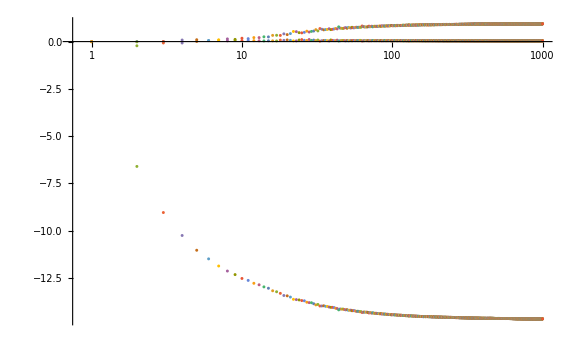

```mathematica
Transpose[lambdaList];
ListLogLinearPlot[lambdaList]
```

```mathematica
(* Looks like the Lyapunov exponents have converged. *)
```

```mathematica
(* Initialization *)
σ = 10; b = 3; r =28;
f[x_, y_, z_] := σ*(y- x);
g[x_, y_, z_] := r*x - y -x*z;
h[x_, y_, z_] := x*y - b*z;
J[x_, y_, z_] := {{D[f[x,y,z],x],D[f[x,y,z],y], D[f[x,y,z],z]}, {D[g[x,y,z],x],D[g[x,y,z],y], D[g[x,y,z],z]},{D[h[x,y,z],x], D[h[x,y,z],y],D[h[x,y,z],z]}};
Tmax = 1000; Tmin = 1;
s=NDSolve[{x'[t]==σ*(y[t]-x[t]),y'[t]==r*x[t]-y[t]-x [t]*z[t],z'[t]==x[t]*y[t] - b*z[t],x[0]==y[0]==z[0]==0.01},{x,y,z},{t,Tmin,Tmax},MaxSteps->1000000];
dt = 0.001;
Q = IdentityMatrix[3];
λ = ConstantArray[0,3];
lambdaList2 = {{0,0,0}};
plotIndex = 0;
(* Main loop *)
For[i=Tmin,i<Tmax,i = i + dt,
trajI ={Evaluate[x[i]/. s],  Evaluate[y[i]/. s],Evaluate[z[i]/. s]};
	Jxt = J[x, y, z] /. {x -> trajI[[1]][[1]], y-> trajI[[2]][[1]], z -> trajI[[3]][[1]]};
	M = IdentityMatrix[3]  + Jxt*dt;
	QR = QRDecomposition[M.Q];
	Qnew = Transpose[QR[[1]]];
	λ[[1]] = λ[[1]]+1/Tmax*Log[Abs[QR[[2]][[1]][[1]]]];
	λ[[2]] = λ[[2]]+1/Tmax*Log[Abs[QR[[2]][[2]][[2]]]];
	λ[[3]] = λ[[3]]+1/Tmax*Log[Abs[QR[[2]][[3]][[3]]]];

	If[Mod[plotIndex, 1000] == 0,lambdaList2 = AppendTo[lambdaList2, {{i, Tmax/i*λ[[1]]}, {i, Tmax/i*λ[[2]]}, {i, Tmax/i*λ[[3]]}}];,f];
	plotIndex = plotIndex + 1;
	
	Q = Qnew;
	]
λ
Total[λ] (* Total should be -14 *)
```

{0.969316,0.0394433,-15.0319}

-14.0231

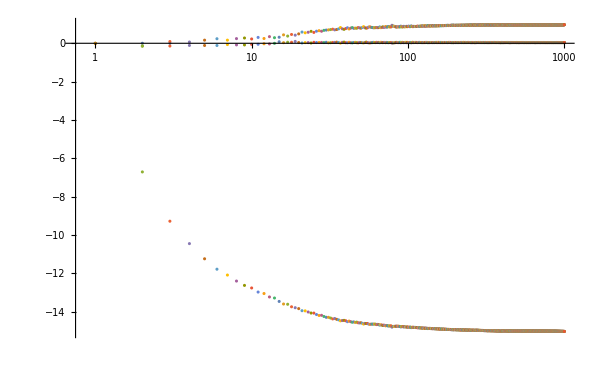

```mathematica
Transpose[lambdaList2];
ListLogLinearPlot[lambdaList2]
```

```mathematica
(* Looks like the Lyapunov exponents have converged. *)
```

```mathematica
(* Initialization *)
σ = 16; b = 5; r =350;
f[x_, y_, z_] := σ*(y- x);
g[x_, y_, z_] := r*x - y -x*z;
h[x_, y_, z_] := x*y - b*z;
J[x_, y_, z_] := {{D[f[x,y,z],x],D[f[x,y,z],y], D[f[x,y,z],z]}, {D[g[x,y,z],x],D[g[x,y,z],y], D[g[x,y,z],z]},{D[h[x,y,z],x], D[h[x,y,z],y],D[h[x,y,z],z]}};
Tmax = 2000; Tmin = 1;
s=NDSolve[{x'[t]==σ*(y[t]-x[t]),y'[t]==r*x[t]-y[t]-x [t]*z[t],z'[t]==x[t]*y[t] - b*z[t],x[0]==y[0]==z[0]==0.01},{x,y,z},{t,Tmin,Tmax},MaxSteps->10000000];
dt = 0.0001;
Q = IdentityMatrix[3];
λ = ConstantArray[0,3];
lambdaList3= {{0,0,0}};
plotIndex = 0;
(* Main loop *)
For[i=Tmin,i<Tmax,i = i + dt,
trajI ={Evaluate[x[i]/. s],  Evaluate[y[i]/. s],Evaluate[z[i]/. s]};
	Jxt = J[x, y, z] /. {x -> trajI[[1]][[1]], y-> trajI[[2]][[1]], z -> trajI[[3]][[1]]};
	M = IdentityMatrix[3]  + Jxt*dt;
	QR = QRDecomposition[M.Q];
	Qnew = Transpose[QR[[1]]];
	λ[[1]] = λ[[1]]+1/Tmax*Log[Abs[QR[[2]][[1]][[1]]]];
	λ[[2]] = λ[[2]]+1/Tmax*Log[Abs[QR[[2]][[2]][[2]]]];
	λ[[3]] = λ[[3]]+1/Tmax*Log[Abs[QR[[2]][[3]][[3]]]];

	If[Mod[plotIndex, 10000] == 0,lambdaList3 = AppendTo[lambdaList3, {{i, Tmax/i*λ[[1]]}, {i, Tmax/i*λ[[2]]}, {i, Tmax/i*λ[[3]]}}];,f];
	plotIndex = plotIndex + 1;

	If[Mod[plotIndex, 1500000] == 0,Print[i];,f];
	
	Q = Qnew;
	]
λ
Total[λ] (* Total should be -22 *)
```

151.

301.

451.

601.

751.

901.

1051.

1201.

1351.

1501.

1651.

1801.

1951.

{0.11855,-2.99782,-18.9849}

-21.8642

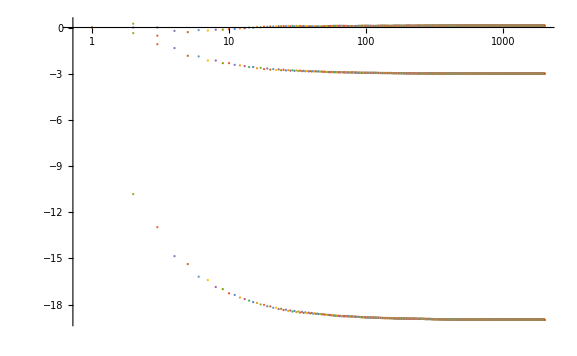

```mathematica
Transpose[lambdaList3];
ListLogLinearPlot[lambdaList3]
```